```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mydata=Import["C:\\Users\\tosta\\Desktop\\Nueva carpeta\\laser.csv"];
```

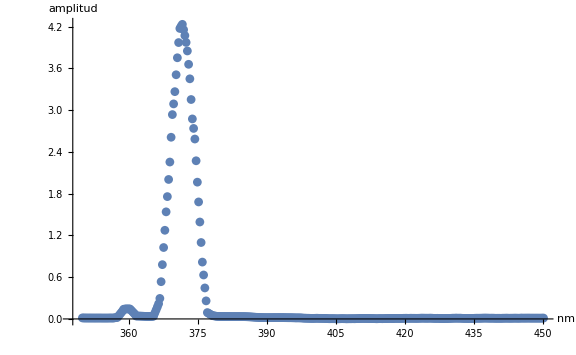

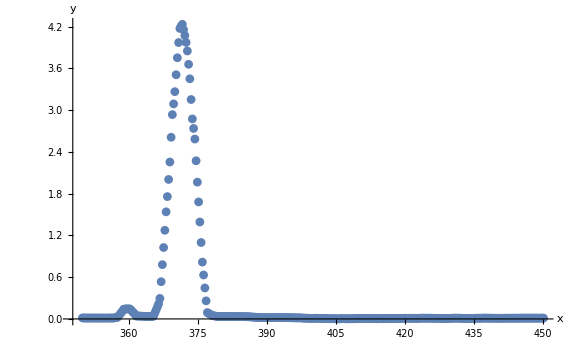

FindMaximum::eqineq: Constraints in {0.0015382,0.00196593,0.00203173,0.00236075,0.00265687,0.00268977,0.00272268,0.00275558,0.00288719,0.00295299,«657»} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

```mathematica
Im1 = ListPlot[mydata,PlotRange->All,ImageSize->Large,AxesLabel->{nm,amplitud},PlotMarkers->{Automatic,9}]
```

```mathematica
Max[mydata,amplitud]
```

Max[450.064,amplitud,nm,amplitud]